#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5(*,1.5*)};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.8)^(-19);
```

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
mn=938.3;
Subscript[α, fine]=1./137.;
hat[l_]:=Sqrt[2 l+1];
resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-sml/results";
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir]
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-sml/results

Real32

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

dipole calculation from B. Gibson & D.R. Lehmann, PRC 13,2 (1976) (T=3/2 only!)
and Golak et al.

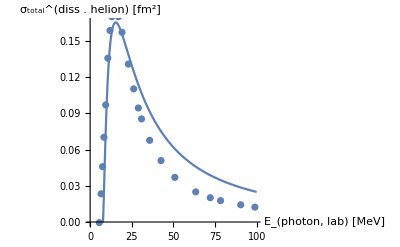

```mathematica
He3DatamBarnGolak=Import["../../../data/he3_photo_diss_sigma_golak.dat","Data"];
He3DatamBarnGibson=Import["../../../data/he3_photo_diss_sigma_gibson.dat","Data"];Bhe=7.67;
He3DataFm2=Transpose[{Transpose[He3DatamBarnGolak][[1]],Transpose[He3DatamBarnGolak][[2]] 10.^(-1)}];

σBethe[ω_,E0_,mM_]:=4 (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,Bhe,938.],{ν,0,100},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . helion) [fm^2]"}],
ListPlot[He3DataFm2,PlotLabel->Style["Gibson - E1",Orange,22]]]
```

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{es=Re[Eigensystem[norm]],ovsqi,ovsq,n},Print["min/max: ",MinMax[es[[1]]]];n=Length[Select[es[[1]],#<cutoff&]];Print["(min/max) discarded elements: ",n," ",MinMax[Select[es[[1]],#<cutoff&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@es[[1]]];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@es[[1]]];
{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}]

normreg[threshold_,noMa_]:=Block[
{es=Eigensystem[noMa],μ,transf},
{μ,transf}=Transpose[Select[Transpose[es],Re[#[[1]]]>threshold&]];
(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the initial state, i.e., J^π=(1/2)^+ for the helion

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}];
```

#### The initial state (helion ground state ^3 He )

only the ground-state energy e0 is used in the remainder of the notebook;
other parts of this section yield analytic information on the initial state

min/max: {2.81772×10^-8,42.8049}

(min/max) discarded elements: 0 {∞,-∞}

B(^3He) = -7.09332

Dim_full^helion = 896=^!896   ;     Dim_(non - singular)^helion = 896

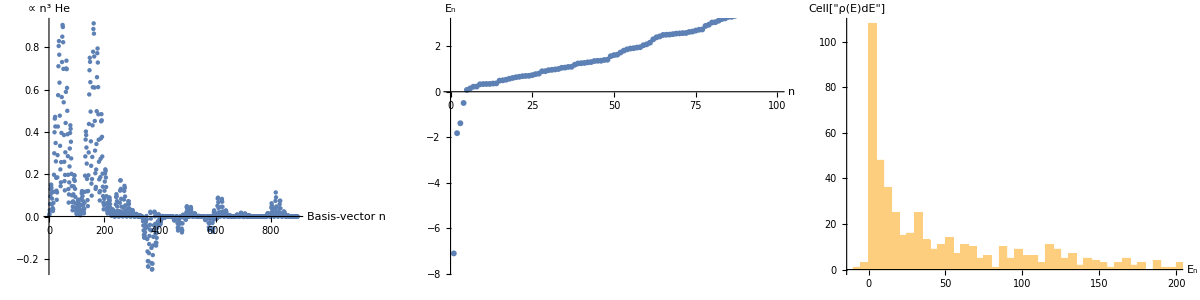

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdLIT];

orderedEVSYHe3=Sort[Transpose[Eigensystem[tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
e0=orderedEVSYHe3[[1,1]];v0=orderedEVSYHe3[[1,2]];

dE=5;
Print["B(^3He) = ",e0];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0][[1]]]

fullv0=Transpose[He3Nmh].v0;
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,AxesLabel->{"Basis-vector n"," ∝ n^3 He"},ImageSize->Large],
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{1.1 e0,3}},AxesLabel->{"n"," E_n"},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{" E_n","Cell["ρ(E)dE",ExpressionUUID->"cf919011-cdda-4cf7-9d6a-392ca1d5a758"]"}]
}}]
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(1/2)^- or J^π=(3/2)^- for the negative-parity rank-1 E_1 operator perturbing a helion;

```mathematica
matnames=("./mat_"<>ToString[#]<>"^-")&/@Subscript[I, n];
LitNormHamMat=readREAL8list[#]&/@matnames;

LITbasisDim=IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat;
LitNorm=ArrayReshape[LitNormHamMat[[#]][[1;;LITbasisDim[[#]]^2]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];LitHam=ArrayReshape[LitNormHamMat[[#]][[LITbasisDim[[#]]^2+1;;]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];
Print["N_final = ",LITbasisDim];
```

N_final = {784}

min/max: {6.30929×10^-6,20.6774}

(min/max) discarded elements: 0 {∞,-∞}

J=0.5:  E_0=-1.96199

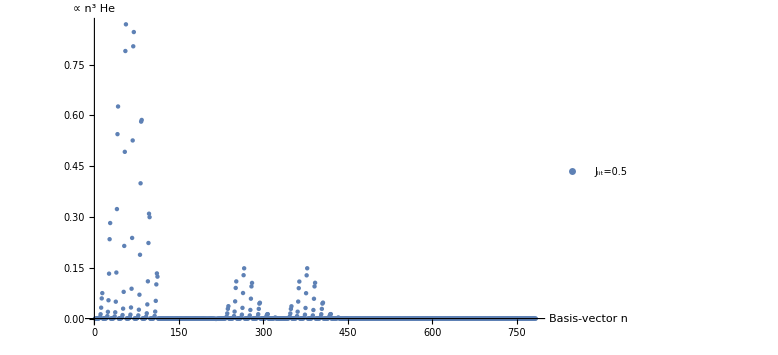
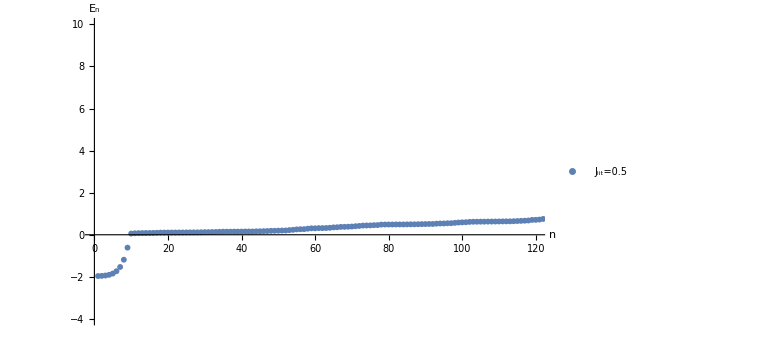
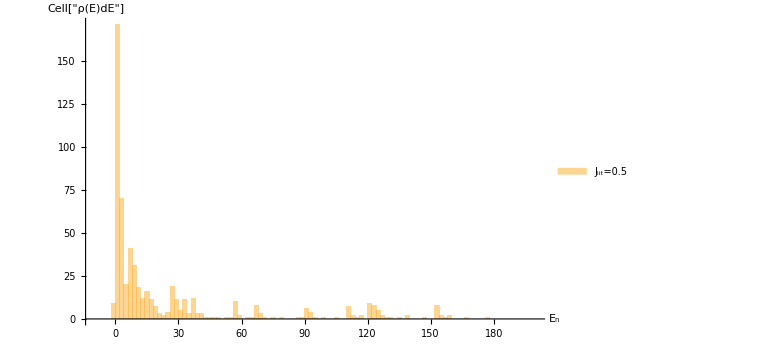
-Graphics- | -Graphics- | -Graphics-

```mathematica
LitNmhis={};
LitEigSys={};
fullv0l={};
dE=2.;
Do[
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]],thresholdLIT];
AppendTo[LitNmhis,{LitNmh,LitNmhi}];
orderedEVSYOut=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
e0l=orderedEVSYOut[[1,1]];v0l=orderedEVSYOut[[1,2]];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];
AppendTo[fullv0l,Transpose[LitNmh].v0l];
AppendTo[LitEigSys,orderedEVSYOut];
,{nj,Range[1,Length[Subscript[I, n]]]}
];

Grid[{{
ListPlot[Re[fullv0l],PlotRange->Full,AxesLabel->{"Basis-vector n"," ∝ n^3 He"},ImageSize->Large,PlotLegends->lege],
ListPlot[#[[All,1]]&/@LitEigSys,PlotRange->{{0,120},{-4,10}},AxesLabel->{"n"," E_n"},ImageSize->Large,PlotLegends->lege],
Histogram[#[[All,1]]&/@LitEigSys,{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{" E_n","Cell["ρ(E)dE",ExpressionUUID->"0684a468-be60-4b73-8dc2-82b8173af1c0"]"},ChartLegends->lege]
}}]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

```mathematica
CouplingBlockj={};
Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

nk=Max[ToExpression[StringSplit[FileNames["*_S_"<>JLIT<>"*"],"_"][[All,1]]]];
ks=Range[0,nk];

CouplingBlock={};
CouplingBlockT={};
Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];

(*CouplingBlocks={};
Do[
Print["(Lm_LJ_0m_I_n-m_l|I_nm_I_n) = (",multipolarity,mL,J0,mIn-mL,"|",Subscript[I, n][[nj]],mIn,")"];
If[Sign[mIn]>=0,mJLIT=StringPadRight[StringDelete[ToString[mIn],"."],2,"0"],mJLIT=StringPadRight[StringDelete[ToString[mIn],"."],3,"0"]];
If[Sign[mL]>=0,mMUL=StringPadRight[StringDelete[ToString[mL],"."],2,"0"],mMUL=StringPadRight[StringDelete[ToString[mL],"."],3,"0"]];

files="./"<>ToString[#]<>"_S_"<>JLIT<>"_"<>mJLIT<>"_"<>mMUL<>".lit"&/@ks;
(*Print[files]*)
inhomos=readREAL8list[#]&/@files;
CouplingMatrices=ArrayReshape[#,{Sqrt[Length[#]],Sqrt[Length[#]]}]&/@inhomos;
CouplingBloxx=#[[He3BasisDim+1;;,;;He3BasisDim]]&/@CouplingMatrices;
dims=Dimensions[#]&/@CouplingBloxx;
coupl=ClebschGordan[{multipolarity,mL},{J0,mIn-mL},{Subscript[I, n][[nj]],mIn}];
(*Print["⟨",multipolarity,mL,J0,mIn-mL,"|",Subscript[I, n][[nj]],mIn,"⟩ =  ",coupl];*)
(*Print[ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],He3BasisDim}]//MatrixForm];*)
AppendTo[CouplingBlocks,coupl ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],He3BasisDim}]];
(*Clear[CouplingBloxx];*)
,{mL,mM}
];
AppendTo[CouplingBlock,{mIn,Total[CouplingBlocks]}];
*)

tmp =BinaryReadList["InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"."<>dt,"Real32"];
OutDim=Dimensions[tmp][[1]]/He3BasisDim;
test=ArrayReshape[tmp,{OutDim,He3BasisDim}];
AppendTo[CouplingBlockT,{mIn,test}];

(*If[Select[Flatten[test],Chop[#,10^-8]==0&]=={},
If[Select[Flatten[Total[CouplingBlocks]/test],Chop[#-1.0,10^-7]≠0.&]≠{},
Print["m_I_n=",mIn,"  : ",Flatten[Total[CouplingBlocks]/test]]//MatrixForm];
];*)

(*Print["m_I_n=",mIn,"  : ",Total[CouplingBlocks]//MatrixForm];*)
,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockj,CouplingBlockT];
(*Clear[CouplingBlock];*)
,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|helion⟩) = ",Dimensions[CouplingBlockj[[#]][[1]][[2]]&/@Range[1,Length[Subscript[I, n]]]]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

Dim(⟨ψ|ο̂|helion⟩) = {1,784,896}

Dim(⟨ψ|Ĥ|ψ⟩) = {1,784,784}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {1,784,784}

#### Analysis of RHS

```mathematica
noCNT=Flatten[Position[λfinal,n_/;n<=0]]
λfinal[[noCNT]]=ConstantArray[43.0,Length[noCNT]]
TakeSmallest[λfinal->"Index",1]
```

{}

{}

{784}

```mathematica
{λsHe,trfHe}=Re[Eigensystem[{He3Ham,He3Norm}]];
evgs=Flatten[trfHe[[TakeSmallest[λsHe->"Index",1]]]];

inhomoGS={};
inhomoCNT={};
mm=1;
nj=1;

tmp=CouplingBlockj[[nj]][[mm]][[2]];

Do[
{λfinal,trfLit}=Re[Eigensystem[{LitHam[[nj]][[;;bv,;;bv]],LitNorm[[nj]][[;;bv,;;bv]]}]];
evgsFgs=Flatten[trfLit[[TakeSmallest[λfinal->"Index",1]]]];

λfinaltmp=λfinal;
noCNT=Flatten[Position[λfinaltmp,n_/;n<=0]];
λfinaltmp[[noCNT]]=ConstantArray[43.0,Length[noCNT]];
evgsFfs=Flatten[trfLit[[TakeSmallest[λfinaltmp->"Index",1]]]];

FgsEi=evgsFgs.(tmp.evgs)[[;;bv]];
FfsEi=evgsFfs.(tmp.evgs)[[;;bv]];

AppendTo[inhomoGS,FgsEi^2];
AppendTo[inhomoCNT,FfsEi^2];
,{bv,Range[LITbasisDim[[1]]]}
]
```

```mathematica
ResourceFunction["MaTeXInstall"][]
```

Paclet[MaTeX,1.7.8,<>]

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

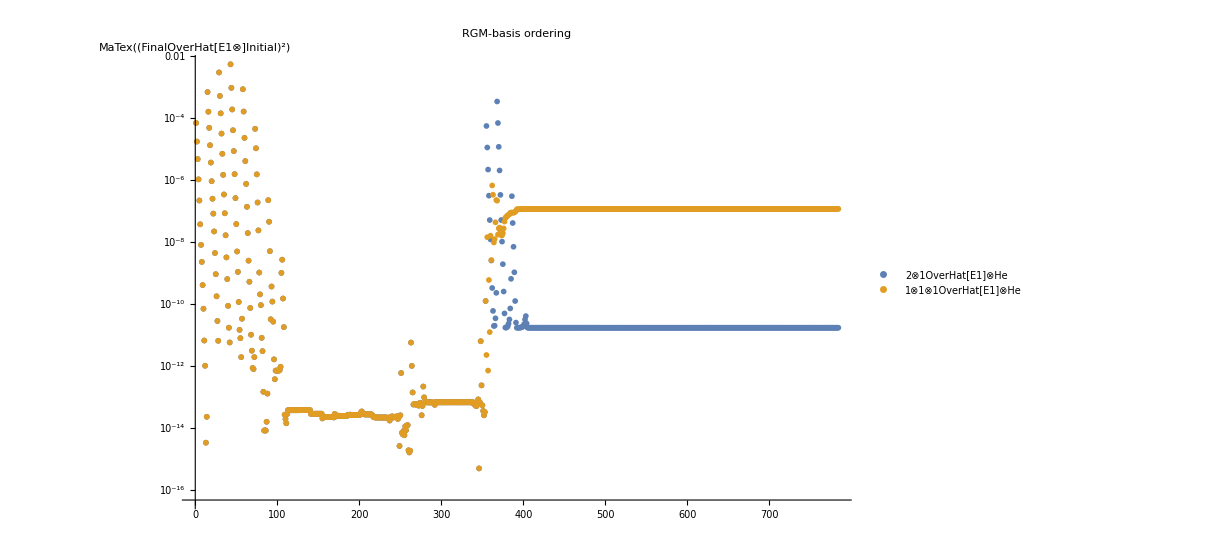

```mathematica
lege={"TemplateBox[{RowBox[{\"2\", \"⊗\", \"1\"}],RowBox[{OverscriptBox[\"E1\", \"^\"], \"⊗\", \"He\"}]},\"BraKet\"]","TemplateBox[{RowBox[{\"1\", \"⊗\", \"1\", \"⊗\", \"1\"}],RowBox[{OverscriptBox[\"E1\", \"^\"], \"⊗\", \"He\"}]},\"BraKet\"]"};
ListLogPlot[{inhomoGS,inhomoCNT},AxesLabel->{MaTeX["\\text{Final-state Basis dimension}",Magnification->2],MaTex["(FinalOverHat[E1⊗]Initial)^2"]},PlotLegends->lege,ImageSize->ImgSize,PlotRange->Automatic,PlotLabel->"RGM-basis ordering"]
```

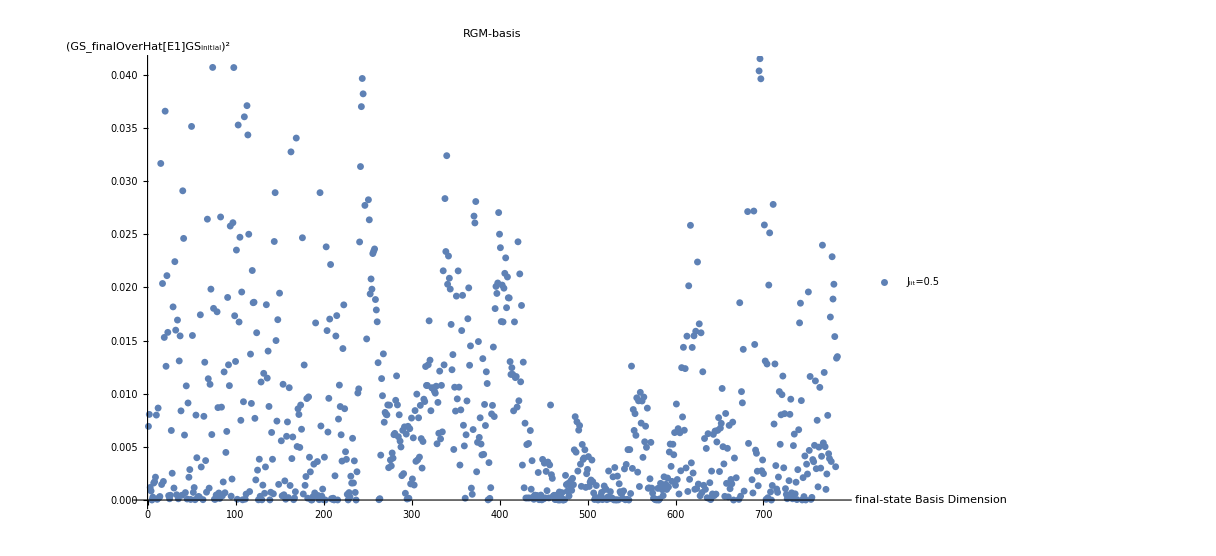

```mathematica
OμRHSEB=normreg[thresholdLIT,He3Norm];
{λsHeEB,trfHeEB}=Re[Eigensystem[(Transpose[OμRHSEB].He3Ham).OμRHSEB]];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];
inhomoEB={};

mm=1;
nj=1;

tmp=CouplingBlockj[[nj]][[mm]][[2]];

Do[
OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]][[;;bv,;;bv]]];
{λfinalEB,trfLitEB}=Re[Eigensystem[(Transpose[OμLHSEB].LitHam[[nj]][[;;bv,;;bv]]).OμLHSEB]];

evgsf=Flatten[trfLitEB[[TakeSmallest[λfinalEB->"Index",1]]]];

fEi=evgsf.(tmp.evgsEB)[[;;bv]];

AppendTo[inhomoEB,fEi^2];
,{bv,Range[LITbasisDim[[1]]]}
]

ListPlot[inhomoEB,AxesLabel->{"final-state Basis Dimension","(GS_finalOverHat[E1]GS_initial)^2"},PlotLegends->lege,ImageSize->ImgSize,PlotRange->Automatic,PlotLabel->"RGM-basis"]
```

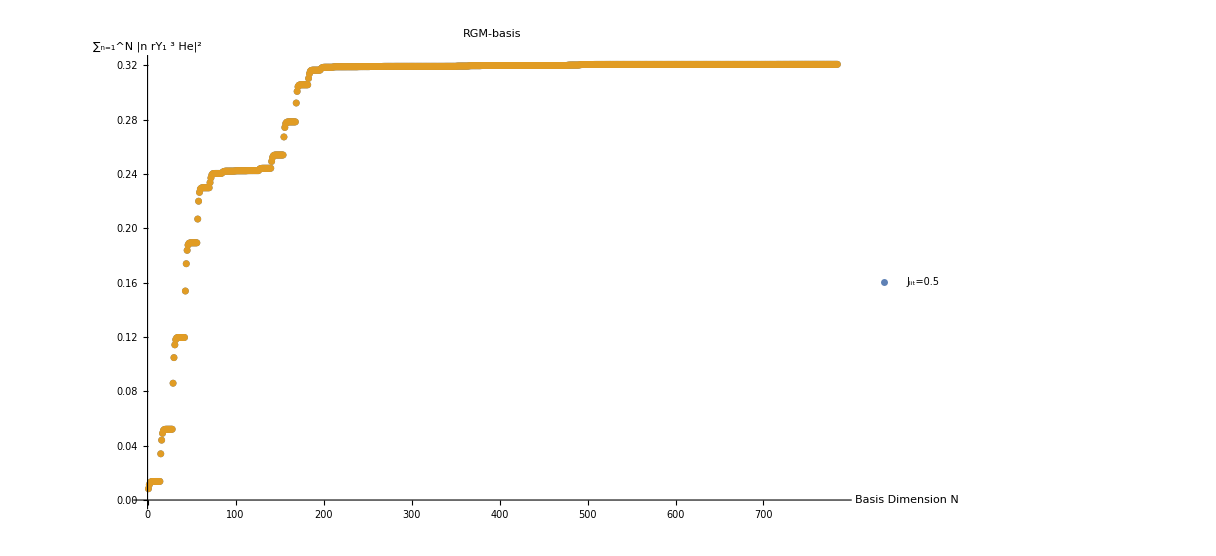
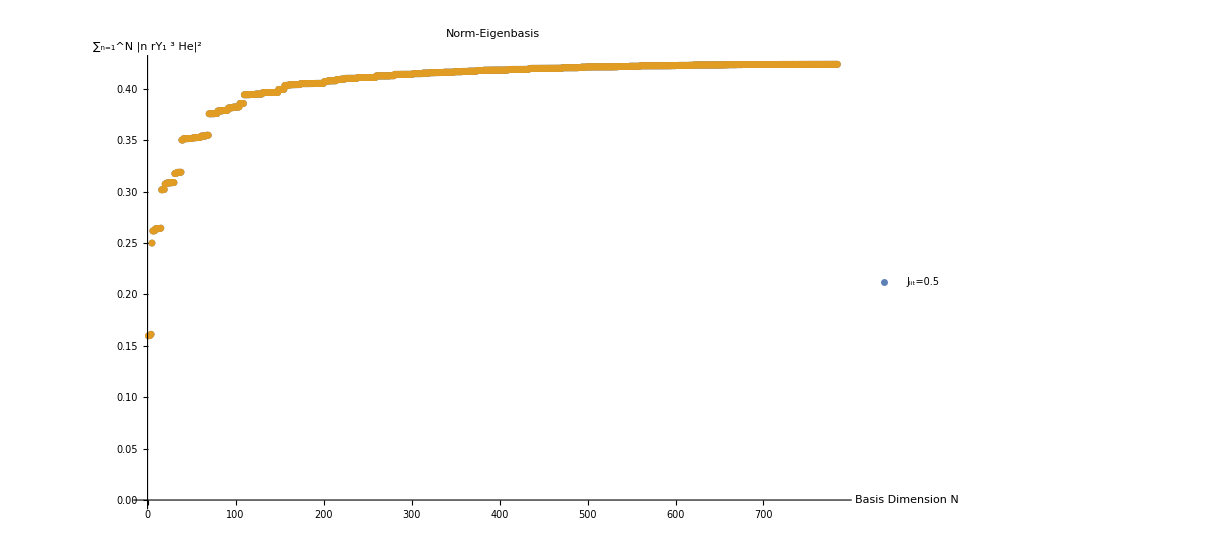
-Graphics- | -Graphics-

```mathematica
OμRHSEB=normreg[thresholdLIT,He3Norm];
{λsHeEB,trfHeEB}=Re[Eigensystem[(Transpose[OμRHSEB].He3Ham).OμRHSEB]];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];
inhomoEB={};

{λsHe,trfHe}=Re[Eigensystem[{He3Ham,He3Norm}]];
evgs=Flatten[trfHe[[TakeSmallest[λsHe->"Index",1]]]];
inhomo={};

Do[
Do[
OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]]];
{λfinalEB,trfLitEB}=Re[Eigensystem[(Transpose[OμLHSEB].LitHam[[nj]]).OμLHSEB]];
tmp=CouplingBlockj[[nj]][[mm]][[2]];
AppendTo[inhomoEB,Transpose[OμLHSEB].((tmp.OμRHSEB).evgsEB)];

{λfinal,trfLit}=Re[Eigensystem[{LitHam[[nj]],LitNorm[[nj]]}]];
AppendTo[inhomo,tmp.evgs];
,{mm,Range[1,Length[mIns[[nj]]]]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
]
mm=1;

inhomonorms=Table[Norm[#[[;;n]]],{n,Length[#]}]&/@inhomo;
inhomonormsEB=Table[Norm[#[[;;n]]],{n,Length[#]}]&/@inhomoEB;
Grid[{{
ListPlot[inhomonorms,AxesLabel->{"Basis Dimension N","Cell[TextData[Cell[BoxData[FormBox[RowBox[{\nSubsuperscriptBox[\"∑\", RowBox[{\"n\", \"=\", \"1\"}], \"N\"], RowBox[{\"|\", RowBox[{\nTemplateBox[{\"n\"},\"Bra\"], \nSubscriptBox[\"rY\", \"1\"], \nTemplateBox[{RowBox[{SuperscriptBox[\"\", \"3\"], \"He\"}]},\"Ket\"]}], \nSuperscriptBox[\"|\", \"2\"]}]}], TraditionalForm]]]]]"},PlotLegends->lege,ImageSize->ImgSize,PlotRange->Full,PlotLabel->"RGM-basis"],
ListPlot[inhomonormsEB,AxesLabel->{"Basis Dimension N","Cell[TextData[Cell[BoxData[FormBox[RowBox[{\nSubsuperscriptBox[\"∑\", RowBox[{\"n\", \"=\", \"1\"}], \"N\"], RowBox[{\"|\", RowBox[{\nTemplateBox[{\"n\"},\"Bra\"], \nSubscriptBox[\"rY\", \"1\"], \nTemplateBox[{RowBox[{SuperscriptBox[\"\", \"3\"], \"He\"}]},\"Ket\"]}], \nSuperscriptBox[\"|\", \"2\"]}]}], TraditionalForm]]]]]"},PlotLegends->lege,ImageSize->ImgSize,PlotRange->Full,PlotLabel->"Norm-Eigenbasis"]
}}
]
```

{-7.09332,-1.81831,-1.38208}

{-7.09332,-1.81831,-1.38208}

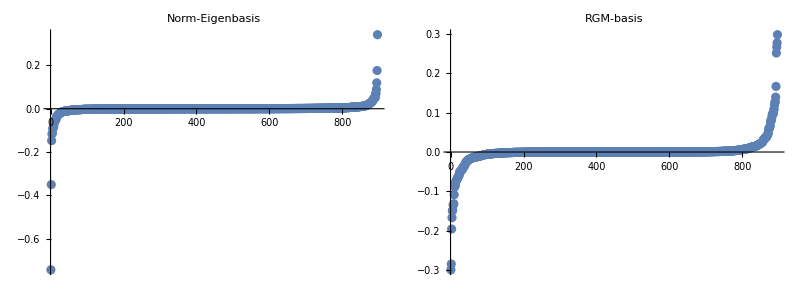

```mathematica
Sort[λsHeEB][[1;;3]]
Sort[λsHe][[1;;3]]
Grid[{{ListPlot[Sort[evgsEB],PlotRange->Full,ImageSize->ImgSize,PlotLabel->"Norm-Eigenbasis"],ListPlot[Sort[evgs],PlotRange->Full,ImageSize->ImgSize,PlotLabel->"RGM-basis"]}}]
```

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

E_0( th=2.31712×10^-20 ) = -136.247    dim(He3,LIT) = {896}{784}

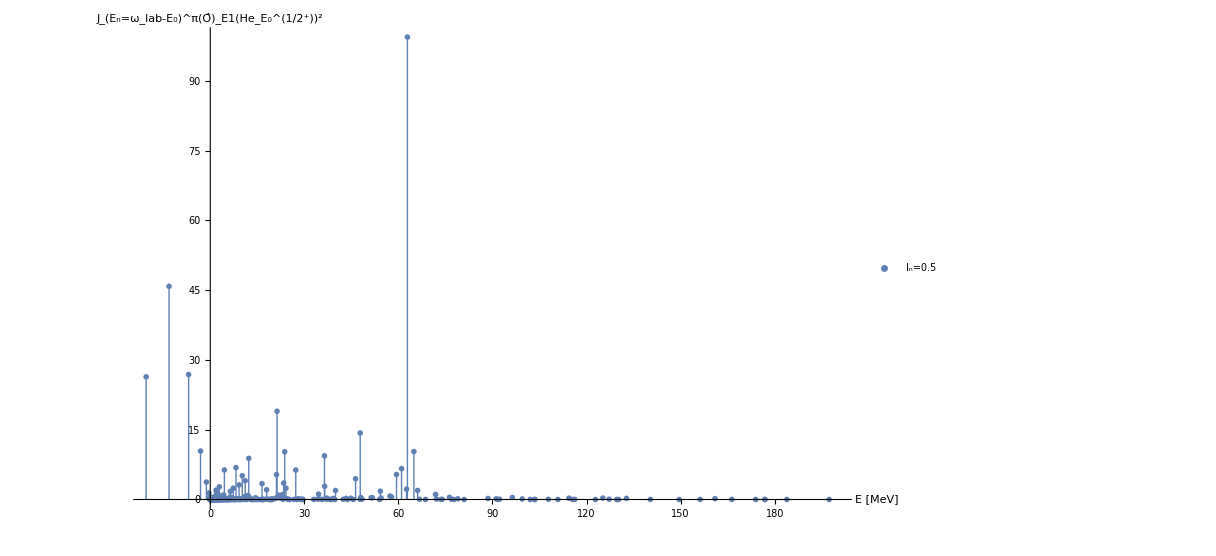
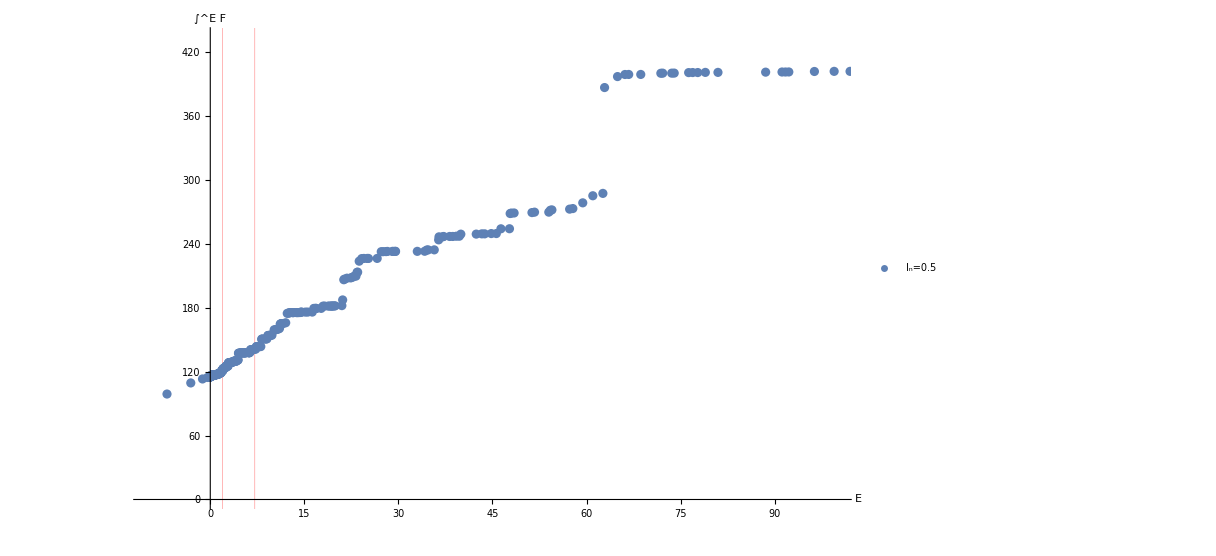

```mathematica
Clear[es,μ,transf];
lpsis={};CumStrengths={};

es=Re[Eigensystem[He3Norm]];
{μ,transf}=Transpose[Select[Transpose[es],Re[#[[1]]]>thresholdLIT&]];
(*OμRHS=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);*)
OμRHS=IdentityMatrix[Dimensions[He3Norm[[1]]][[1]]];

{λsD,trfD}=Eigensystem[(Transpose[OμRHS].He3Ham).OμRHS];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];
egs=Min[λsD];

leg={};

Do[
lpsi={};
esl=Re[Eigensystem[LitNorm[[nj]]]];
{μl,transfl}=Transpose[Select[Transpose[esl],Re[#[[1]]]>thresholdLIT&]];
(*OμLHS=(Transpose[transfl].DiagonalMatrix[μl^(-1/2)]);*)
OμLHS=IdentityMatrix[Dimensions[LitNorm[[1]]][[1]]];
{λfinal,trfLit}=Eigensystem[(Transpose[OμLHS].(LitHam[[nj]])).OμLHS];

Print["E_0( th=",N[thresholdLIT]," ) = ",egs,"    dim(He3,LIT) = ",Dimensions[λsD],Dimensions[λfinal]];

tmpl=0;

Do[
inhomo=(Transpose[OμLHS].(CouplingBlockj[[nj]][[mm]][[2]].OμRHS)).(evgs);
AppendTo[lpsi,Transpose[{λfinal(*+Abs[egs]*),(trfLit.inhomo)^2}]];
tmpl = tmpl + (trfLit.inhomo)^2;
,{mm,Length[mIns[[nj]]]}
];

AppendTo[lpsis,Re[Transpose[{λfinal,tmpl}]]];
AppendTo[CumStrengths,Re[Transpose[{Sort[lpsis[[nj]]][[All,1]],Accumulate[Sort[lpsis[[nj]]][[All,2]]]}]]];

AppendTo[leg,"I_n="<>ToString[Subscript[I, n][[nj]]]];

(*AppendTo[lpsis,Flatten[lpsi,1]];*)

,{nj,Range[1,Length[Subscript[I, n]]]}
]


plote3=Grid[{{
ListPlot[lpsis,Joined->False,PlotMarkers->{{♔,12},{♗,12}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{{-20,200},Full},AxesLabel->{Style["E [MeV]",18],Style["Cell[TextData[Cell[BoxData[RowBox[{\nTemplateBox[{SubsuperscriptBox[\"J\", RowBox[{SubscriptBox[\"E\", \"n\"], \"=\", RowBox[{SubscriptBox[\"ω\", \"lab\"], \"-\", SubscriptBox[\"E\", \"0\"]}]}], \"π\"]},\"Bra\"], \nSubscriptBox[\nOverscriptBox[\"O\", \"^\"], \"E1\"], \nSuperscriptBox[\nTemplateBox[{SubsuperscriptBox[\"He\", SubscriptBox[\"E\", \"0\"], RowBox[{\"1\", \"/\", SuperscriptBox[\"2\", \"+\"]}]]},\"Ket\"], \"2\"]}]]]]]",18]},PlotStyle->{},PlotLegends->leg,ImageSize->ImgSize]
},{
ListPlot[CumStrengths,Joined->False,ImageSize->ImgSize,PlotRange->{{-10,100},Automatic},PlotLegends->leg,GridLines->{{{Abs[e0],Red},{Abs[e0l],Red}},None},AxesLabel->{Style["E",18],Style["Cell[TextData[{\nCell[BoxData[FormBox[\nOverscriptBox[\"∫\", \"E\"], TraditionalForm]]],\n\"F\"\n}]]",18]}]
}}]
(*Save[tmpDir<>"/lpsis.plot_"<>ToString[IntegerPart[AbsoluteTime[Now]-AbsoluteTime[Today]]],lpsis]
Save[tmpDir<>"/CumStrength.plot_"<>ToString[IntegerPart[AbsoluteTime[Now]-AbsoluteTime[Today]]],CumStrengths]
Export["delta_strength_function_helion.pdf",plote3,"PDF","AllowRasterization"->False]*)
```

#### S(E)=∑_m Ψ_m^2·δ(E-λ_m) → S_benign(E)

C(E):=∫E/0 dΔ S(Δ)=∑_(N_(n,d)) Poly[E,N_numerator]/Poly[E,N_denominator-1]
s.t. C_N/C_M=C(λ_(f,max))  (saturation criterium for equal polynomial orders in numerator and denominator)
F(E)=(∂C)/(∂E)

```mathematica
Put[CumStrengths,LocalObject["CumHelionStrengths"]]
```

LocalObject[file:///home/kirscher/.Wolfram/Objects/CumHelionStrengths]

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 5500 iterations.

{(t^2 (379.775 t^2+27897.3 t+556305.))/(1. t^4+12.923 t^3+9014.31 t^2+13365.3 t+13.2008)}

{Piecewise[{{(-22989.5 t^6+7.57746×10^6 t^5-1.85199×10^8 t^4-1.789×10^9 t^3+1.07761×10^11 t^2-1.30327×10^12 t+5.24917×10^12)/((1. t^4-40.5293 t^3+9567.67 t^2-230175. t+1.43216×10^6)^2), t≥13.3631}, {0, True}}]}

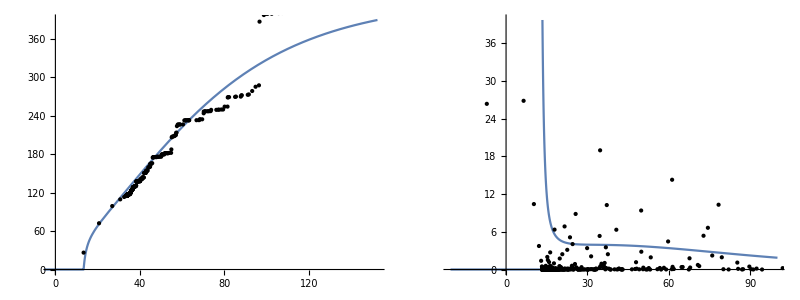

```mathematica
data=CumStrengths;
offsets=Min[#[[All,1]]]&/@data;
dataShifted=Transpose[{#[[All,1]]-#[[All,1]][[1]],#[[All,2]]}]&/@CumStrengths;
data=dataShifted;
ordnum=4;orddenom=ordnum-1;
coffs={Array[cnum,ordnum],Array[cdenom,orddenom+1]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{0.0001,0.2},Length[Flatten[coffs]]]}];

(*num=Sum[coffs[[1]][[n]] (t)^n,{n,ordnum}]&/@Range[Length[data]];
denom=1+Sum[coffs[[2]][[n]] (t)^n,{n,orddenom}]&/@Range[Length[data]];*)
num=Sum[coffs[[1]][[n]] (t)^n,{n,2,ordnum}]&/@offsets;
denom=1+coffs[[2]][[-1]] (t)^ordnum+Sum[coffs[[2]][[n]] (t)^n,{n,orddenom}]&/@offsets;

model=num/denom;
constr=#>10.2^(-2)&/@Flatten[coffs];(*10.1^2>#>10.2^(-2)&/@Flatten[coffs];*)
constraints=Union[constr,{Abs[coffs[[1]][[-1]]/coffs[[2]][[-1]]-data[[#]][[-1]][[2]]]<10.^(-9)}]&/@Range[Length[data]];

wgts=Abs[Flatten[Join[{Differences[data[[#]]][[All,2]][[1]],Differences[data[[#]]][[All,2]]}]]&/@Range[Length[data]]];
splitPoint=25;
origFac=112.;
tailFac=221.;

wgt2=Join[origFac #[[;;splitPoint]],#[[1+splitPoint;;-splitPoint]],tailFac #[[-splitPoint+1;;]]]&/@wgts;

optPOSsol=
NonlinearModelFit[dataShifted[[#]],{model[[#]],constraints[[#]]},inicoffs,t,Weights->wgt2[[#]],MaxIterations->5500]&/@Range[Length[data]];

CumFit[ee_]:=Piecewise[ {{optPOSsol[[#]][ee-Abs[e0-offsets[[#]]]],ee≥Abs[e0-offsets[[#]]]},{0,ee<Abs[e0-offsets[[#]]]}}]&/@Range[Length[optPOSsol]]
StC[em_]:=Piecewise[{{D[optPOSsol[[#]][t],t]/.t->(em-Abs[e0-offsets[[#]]]),em≥Abs[e0-offsets[[#]]]},{0,em<Abs[e0-offsets[[#]]]}}]&/@Range[Length[data]]

Simplify[#[t]]&/@optPOSsol//TraditionalForm
Simplify[#]&/@StC[t]//TraditionalForm

percPlot =0.01;
Grid[{{
Plot[CumFit[t][[#]]&/@Range[Length[data]],{t,Min[offsets],percPlot Max[#[[All,1]][[-1]]&/@data]},Epilog->{PointSize[Small],Point[Transpose[{data[[#]][[All,1]]+Abs[e0-offsets[[#]]],data[[#]][[All,2]]}]]&/@Range[Length[data]]},PlotRange->{{-2.3,percPlot Max[#[[All,1]][[-1]]&/@data]},{0,Automatic}},ImageSize->ImgSize],
Plot[StC[e2],{e2,Min[offsets],100},Epilog->Map[Point,Transpose[{lpsis[[#]][[All,1]]+Abs[e0-offsets[[#]]],lpsis[[#]][[All,2]]}]&/@Range[Length[data]]],PlotRange->Full,ImageSize->ImgSize]
}}]
```

#### σ_tot=(2π)^2 α·E_γ ∑_(J,M) JM OverHat[E1](J_0 m_0)^2

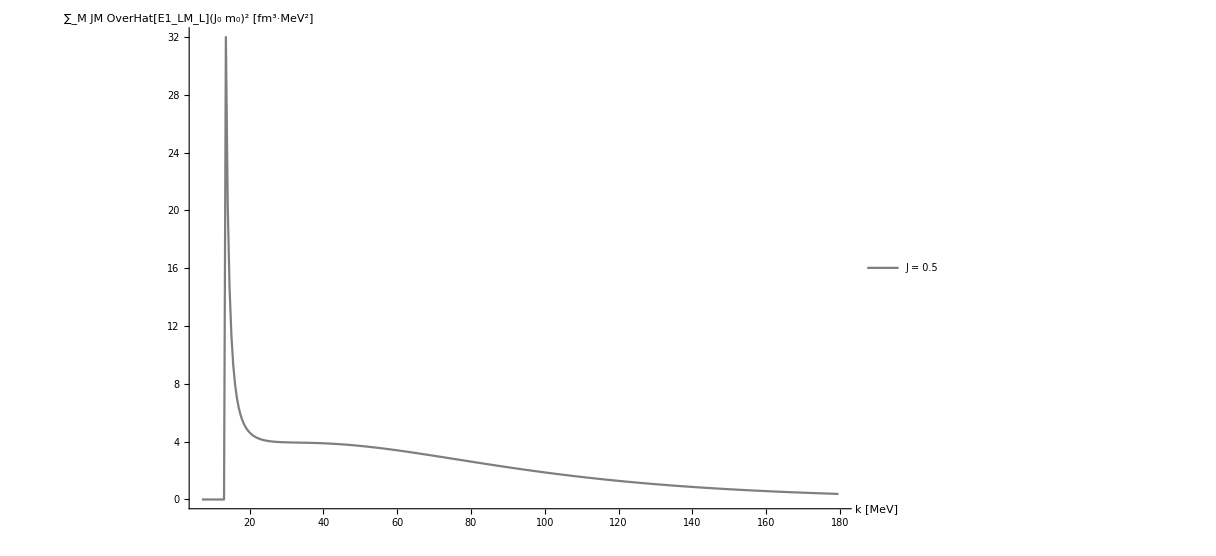
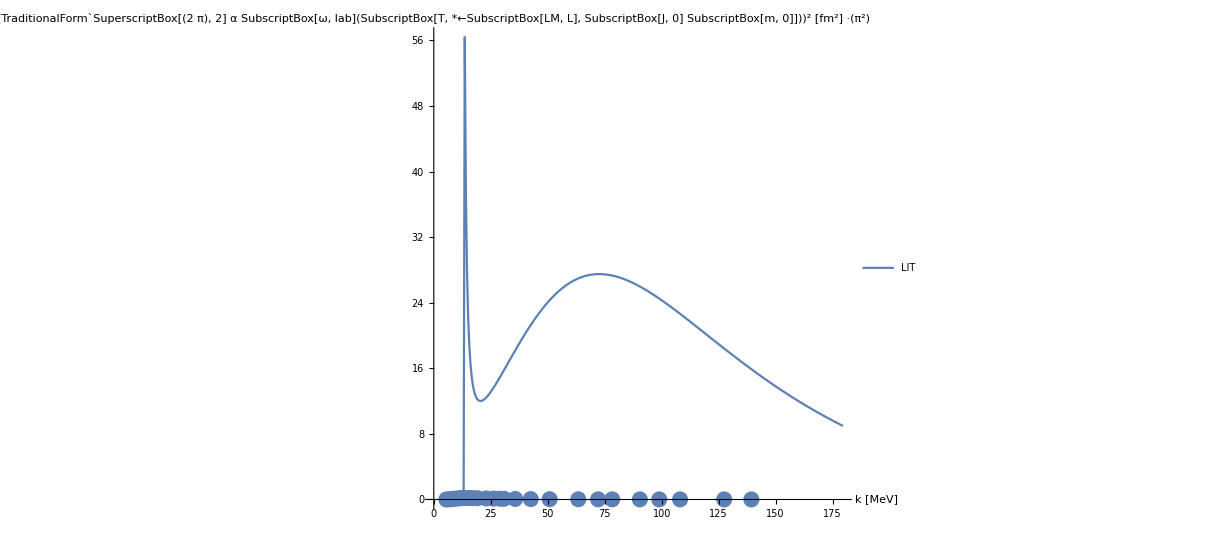
-Graphics- | -Graphics-

```mathematica
Clear[ee,e2];
k0=0.001;k1=180;dK=0.5;
Subscript[k, lab]=Range[Abs[e0],k1,dK];
Ji=Jf=J0;Mi=Ji;Mf=Mi;

labelj=("J = "<>ToString[#])&/@Subscript[I, n];
responseListJ=StC[t];
strengthfunctionList=Table[Table[(responseListJ[[nJ]]/.t->ee)/.ee->kmag,{kmag,Subscript[k, lab]}],{nJ,Range[1,Length[Subscript[I, n]]]}];

z=List[];

For[nJ=1,nJ≤Length[Subscript[I, n]],nJ++,(
atmp=ListLinePlot[strengthfunctionList[[nJ,All]],PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","FormBox[RowBox[{UnderscriptBox[\"∑\", \"M\"], RowBox[{TemplateBox[{\"JM\"},\"Bra\"], OverscriptBox[SubscriptBox[\"E1\", SubscriptBox[\"LM\", \"L\"]], \"^\"], SuperscriptBox[TemplateBox[{RowBox[{SubscriptBox[\"J\", \"0\"], SubscriptBox[\"m\", \"0\"]}]},\"Ket\"], \"2\"]}]}],TraditionalForm] [fm^3·MeV^2]"},ImageSize->ImgSize,Joined->True,DataRange->{Min[Subscript[k, lab]],Max[Subscript[k, lab]]},PlotStyle->{ColorData[7,"ColorList"][[nJ]]},PlotLegends->{labelj[[nJ]]}];
AppendTo[z,atmp];
)];

Tsquared[Mf_,Mi_,λf_,θ_]:=
Module[{compo},
ampli=0;
For[nJ=1,nJ≤Length[Subscript[I, n]],nJ++,
compo=strengthfunctionList[[nJ,All]];
For[Mm=-multipolarity,Mm≤multipolarity,Mm++,
For[Mmp=-multipolarity,Mmp≤multipolarity,Mmp++,
ampli+=compo;
];
];];
Return[ampli]
]
fudgi=Pi^2;

kinfac=fudgi (2 Pi)^2 Subscript[α, fine] (Subscript[k, lab])/hbarc;

DissCross[Mf_,Mi_,λf_,kinfac_]:=kinfac Tsquared[Mf,Mi,λf,θ];
lf=1;

Grid[{{
Show[z,PlotRange->All],
Show[ListPlot[Re[DissCross[Jf,Ji,lf,kinfac]],PlotRange->{Automatic,{0,Full}},LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`SuperscriptBox[(2  π), 2] α SubscriptBox[ω, lab](SubscriptBox[T, *←SubscriptBox[LM, L], SubscriptBox[J, 0] SubscriptBox[m, 0]]))^2 [fm^2] ·("<>ToString[Style[fudgi,Red],TraditionalForm]<>")"}(*,Filling->cycl*),ImageSize->ImgSize,Joined->{True,False},DataRange->{Min[Subscript[k, lab]],Max[Subscript[k, lab]]},PlotLegends->{"LIT"}],
ListPlot[He3DataFm2,PlotLegends->"σ_tot data"]]
}}]
```

d^5 σ_(He→npp)=(2π)^2 α ω_lab ∑|p_1 q_1Ô(ω)He|^2 d^3(p_1,q_1)δ(p_1^2+3/4 q_1^2-ω)

```mathematica
Clear[solu,wcm,wlab,wcem]
solu=Solve[wcm==wlab (1+2 wlab/mdeu)^(-1/2),wlab];
wl=Simplify[wlab/.solu[[2]]]

kcross=0.5 Sqrt[(wcem+e0-2 mn)(wcem+e0+2 mn)]
```

(wcm^2+√(wcm^2 (mdeu^2+wcm^2)))/mdeu

0.5 √((-1883.69+wcem) (1869.51+wcem))